LAGRANGE INTERPOLATION MODULE

==================================================================================
CODE6 .1-LagrangeP.nb.A Mathematica (nb) module implementing Pseudocode 6.1.                   
  
 NUMERICAL METHODS FOR SCIENTISTS AND ENGINEERS: WITH PSEUDOCODES
   First Edition. (c) By Zekeriya ALTAÇ (2024).
   ISBN: 978-1-032-75474-1 (hbk)
   ISBN: 978-1-032-75642-4 (pbk)
   ISBN: 978-1-003-47494-4 (ebk)
   
   DOI : 10.1201/9781003474944
   C&H/CRC PRESS, Boca Raton, FL, USA & London, UK.
   
 This free software is complimented by the author to accompany the textbook.
 E-mail: altacz@gmail.com.
   
DESCRIPTION: A module to compute the Lagrange polynomials at any x.  
                                                                                               
ON ENTRY                                                                                     
        data  :: Data set containing (x_k, f_k,) for k=0,1,2,...,n.  
                                                                                               
ON RETURN                                                                                     
        L_k(x) :: Array of length (n+1) containing Lagrange polynomials that is, L(k)=L_k(xval) for k=0,1,2,...,n.                                                                  
                                                                                               
REVISION DATE :: 02/28/2025                                                                  
 ==================================================================================

```mathematica
LagrangeP[data0_]:=
Module[{data=N[data0],j,k,n},
Subscript[X, k_] := Transpose[data]_⟦1,k+1⟧; (* Subsript is set as from 0 to n  *)
n = Length[data]-1; 
For[ k=0, k≤n, k++,
L[k,x_] = ( ∏_(j=0)^(k-1) (x-Subscript[X, j])/(Subscript[X, k]-Subscript[X, j]))(∏_(j=k+1)^n (x-Subscript[X, j])/(Subscript[X, k]-Subscript[X, j]));Print[Subscript["L", k],"(x)= ",L[k,x]]  ];  (* j=k is skipped *)
];
```

==================================================================================
CODE6 .1-LagrangeEval.nb.A Mathematica (nb) module implementing Pseudocode 6.1.                   
  
 NUMERICAL METHODS FOR SCIENTISTS AND ENGINEERS: WITH PSEUDOCODES
   First Edition. (c) By Zekeriya ALTAÇ (2024).
   ISBN: 978-1-032-75474-1 (hbk)
   ISBN: 978-1-032-75642-4 (pbk)
   ISBN: 978-1-003-47494-4 (ebk)
   
   DOI : 10.1201/9781003474944
   C&H/CRC PRESS, Boca Raton, FL, USA & London, UK.
   
 This free software is complimented by the author to accompany the textbook.
 E-mail: altacz@gmail.com.
   
DESCRIPTION: A function module to evaluate the Lagrange interpolating polynomial for an arbitrary xval, f=f (xval)=fval within x_0<= xval <= x_n. 
                                                                                               
ARGUMENTS                                                                                                                 
     xval ::  x value at which the dataset is to be interpolated;                                   
    data  :: Data set containing (x_k, f_k,) for k=0,1,2,...,n.                                                               
                                                                                               
REVISION DATE :: 02/28/2025                                                                  
 ==================================================================================

```mathematica
LagrangeEval[xval0_,data0_]:=
Module[{xval=xval0,data=data0,k,n,X,Y},
LagrangeP[data];
Subscript[Y, k_] := Transpose[data]_⟦2,k+1⟧; 
n = Length[data]-1; 
fval=∑_(k=0)^n Subscript[Y, k] L[k,xval] ;Return[{xval,fval}];];
```

TEST PROBLEM

Supply discrete dataset below:

```mathematica
dataset={{0,3},{0.5,3.625},{1,5},{1.5,7.875},{2,13}}
```

{{0,3},{0.5,3.625},{1,5},{1.5,7.875},{2,13}}

Generate Lagrange Polynomials using LagrangeP[data]

```mathematica
LagrangeP[dataset ]
```

L_0(x)= 0.666667 (-2.+x) (-1.5+x) (-1.+x) (-0.5+x)

L_1(x)= -2.66667 (-2.+x) (-1.5+x) (-1.+x) (0.+x)

L_2(x)= 4. (-2.+x) (-1.5+x) (-0.5+x) (0.+x)

L_3(x)= -2.66667 (-2.+x) (-1.+x) (-0.5+x) (0.+x)

L_4(x)= 0.666667 (-1.5+x) (-1.+x) (-0.5+x) (0.+x)

Evaluate Lagrange Interpolating Polynomial for an arbitrary xval using LagrangeEval[x,dataset]; the output is {xval, fval}.

```mathematica
xval=0.64; LagrangeEval[xval,dataset]
```

L_0(x)= 0.666667 (-2.+x) (-1.5+x) (-1.+x) (-0.5+x)

L_1(x)= -2.66667 (-2.+x) (-1.5+x) (-1.+x) (0.+x)

L_2(x)= 4. (-2.+x) (-1.5+x) (-0.5+x) (0.+x)

L_3(x)= -2.66667 (-2.+x) (-1.+x) (-0.5+x) (0.+x)

L_4(x)= 0.666667 (-1.5+x) (-1.+x) (-0.5+x) (0.+x)

{0.64,3.90214}

GENERATE PLOTS

Plot Discrete Dataset

```mathematica
BBlue=RGBColor[0,0.25,0.82];
Linethickness=Thickness[0.010]
```

Thickness[0.01]

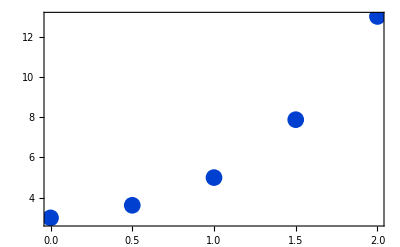

```mathematica
Xs=Table[dataset[[i,1]],{i,1,Length[dataset]}];minvalue=Min[Xs];maxvalue=Max[Xs];points=ListPlot[dataset, 
PlotStyle->{BBlue,AbsolutePointSize[12]},
LabelStyle->Directive[Black,Large],
Frame->True,
PlotRangePadding-> (maxvalue-minvalue)/10, 
FrameStyle->Directive[Black,Thick,20]]
```

Plot Lagrange Interpolating Polynomial

```mathematica
Subscript[Y, k_] := Transpose[dataset]_⟦2,k+1⟧;
n = Length[dataset]-1;
IntFunc[x_]:=∑_(k=0)^n Subscript[Y, k] L[k,x]  (* Construct a continious interpolating polynomial *)
```

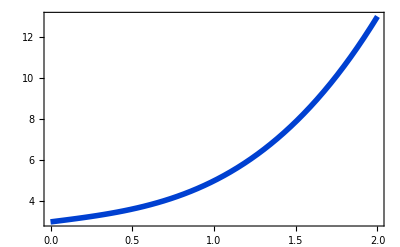

```mathematica
plt=Plot[IntFunc[x],{x,minvalue,maxvalue},
PlotStyle->{BBlue,Linethickness}, 
LabelStyle->Directive[Black,Large], 
Frame->True, 
PlotRangePadding-> (maxvalue-minvalue)/10,
FrameStyle->Directive[Black,Thick,20]]
```

Plot Interpolating Polynomial along with the dataset

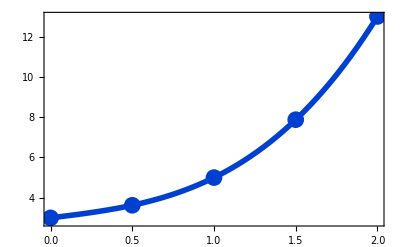

```mathematica
Show[points,plt]
```

Plot Lagrange Polynomials

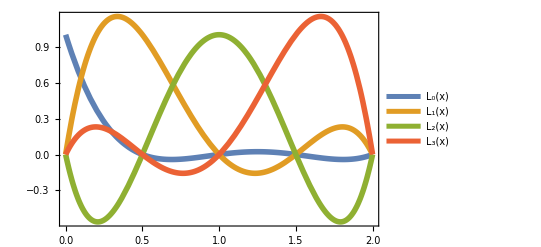

```mathematica
plt=Plot[{L[0,x],L[1,x],L[2,x],L[3,x]},{x,minvalue,maxvalue},
PlotStyle->{Linethickness}, 
LabelStyle->Directive[Black,Large], 
Frame->True, 
PlotLegends->{Style["L_0(x)",16],Style["L_1(x)",16],Style["L_2(x)",16],Style["L_3(x)",16]},
PlotRangePadding-> (maxvalue-minvalue)/10,
FrameStyle->Directive[Black,Thick,20]]
```